```mathematica
ClearAll["Global`*"]
```

# Time-dependent Hamiltonian for a two-level system:

applications in a variety of different areas, including NMR, laser physics, quantum information,

```mathematica
-Graphics-;
```

### Hamiltonian

```mathematica
ham[e1_,e2_,b_,omega_,t_]:={{e1,b*Cos[omega*t]},{b*Cos[omega*t],e2}}
```

### parameters

```mathematica
e1=1.;
e2=-e1;
b=.1;
omega=1.8;
dtstep=0.1;
```

```mathematica
initialstate=({{1}, {0}});
```

```mathematica
h[t_]:=ham[e1,e2,b,omega,t]
```

```mathematica
h[t]//MatrixForm
```

(1. | 0.1 Cos[1.8 t]
0.1 Cos[1.8 t] | -1.)

### Time evolution

```mathematica
ClearAll@constructU;
constructU::usage="constructU[h,tinit,tfinal,n]";
constructU[h_,tinit_,tfinal_,n_]:=Module[
{
dt=N[(tfinal-tinit)/n],
curVal=IdentityMatrix[Length@h[0]]
},
Do[
curVal=MatrixExp[-I*h[t]*dt].curVal,
{t,tinit,tfinal-dt,dt}
];curVal]
```

```mathematica
??constructU
```

```mathematica
Manipulate[
constructU[h,0,t,10]//MatrixForm,
{{t,0.},0.,10.,.1}]
```

```mathematica
Manipulate[
Abs[ConjugateTranspose[initialstate].constructU[h,0,t,10000].initialstate]^2,
{{t,0.},0.,100.,.1}]
```

```mathematica
(*Table[{t,(Abs[ConjugateTranspose[initialstate].constructU[h,0,t,10000].initialstate]^2)[[1,1]]},
{t,0.,100.,.01}]//ListPlot*)
```

### faster

```mathematica
finaltime=100;
Nsteps=Round[finaltime/dtstep];
```

```mathematica
vec=Table[0,{Nsteps}];
vec[[1]]=initialstate;For[i=2,i≤Nsteps,i++,vec[[i]]=MatrixExp[-I*h[(i-1) dtstep]*dtstep].vec[[i-1]]];
```

#### projection onto initial state

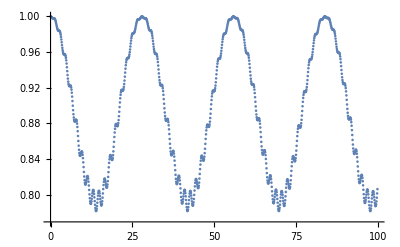

```mathematica
finalevolution=Table[{(i-1) dtstep,(Abs[ConjugateTranspose[vec[[i]]].initialstate]^2)[[1,1]]},
{i,Nsteps}];
ListPlot[finalevolution,PlotRange->All]
```

#### projection onto other state

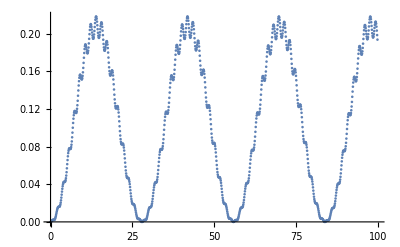

```mathematica
finalevolution=Table[{(i-1) dtstep,(Abs[ConjugateTranspose[vec[[i]]].({{0}, {1}})]^2)[[1,1]]},
{i,Nsteps}];
ListPlot[finalevolution,PlotRange->All]
```

### Check

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

;

-Graphics-;

```mathematica
-Graphics-;
```